I rebuilt our payoff expressions such that they include a v1 mutant whose frequency is denoted as m. For later steps it will also be necessary to redefine alpha’ in terms of alpha. I chose the simplest possible relationship between alpha and alpha’:  alpha’=1-alpha. I then reformulated my payoff expressions in terms of this function and the new specialist 1 mutant m:

```mathematica
ClearAll[d]
(* v = specialist 1 frequency, p = specialist 2 frequency, m = mutant specialist 1, frequency Α = alpha, δ = alpha_g s = specialist carbon sharing, g = generalist carbon sharing *)
S1 = v*s*(1−Α)+m*s*(1−(Α+d))+p*s*(1−(1-Α))+(1−v-m−p)*g*(1−δ);
S2 = (v)*s*(1-(1-Α))+(m)*s*(1−(1-(Α+d)))+p*s*(1−Α)+(1−v-m−p)*g*(1−δ);
S = u*(1-u)*(S1-S2);
S = Simplify[S]
H1=s*u*(Α−1)+(1−u)*s*((1-Α)−1);
HM = s*u*((Α+d)−1)+(1−u)*s*((1-(Α+d))−1);
H2 = s*u*((1-Α)−1)+(1−u)*s*(Α−1);
HG =g*(δ−1);
Hbar = v*H1+p*H2+(1-v-p-m)(HG)+m*HM;
V=v(H1-Hbar);
V=Simplify[V]
P = p(H2-Hbar);
P = Simplify[P]
M = m(HM-Hbar);
M = Simplify[M]
```

s (-1+u) u (-(p-v) (-1+2 Α)+m (-1+2 d+2 Α))

-s v (d m (-1+2 u)+p (-1+u+Α-2 u Α)+(-1+m+v) (-u-Α+2 u Α))+g v (-1+m+p+v) (-1+δ)

p (s (-1+p+u+m u-p u+d (m-2 m u)+u v+Α+m Α-p Α-2 u Α-2 m u Α+2 p u Α+v Α-2 u v Α)+g (-1+m+p+v) (-1+δ))

m (s (d (-1+m+2 u-2 m u)-(-1+m+v) (-u-Α+2 u Α)+p (1-u-Α+2 u Α))+g (-1+m+p+v) (-1+δ))

A note: the v1 specialists and v1 mutants are not in direct competition with eachother i.e. increase in the frequency of the mutant does not explicitly decrease the payoff received by the v1 host as part of its payoff expression, though it does decrease the symbiont reserve from which the v1 host can draw from. I could potentially put them in direct competition though I’m not sure if this makes sense conceputally.

The specialist 1 mutant has a value of alpha which varies by the quantity d. Increases in d increase matching payoff, while decreasing mismatch payoff.

Next I defined out system of replicators using these expressions. My system begins without mutants thus m at t=0 is 0. I let this system run for 3000 timesteps to allow it to settle into a stable limit cycle:

```mathematica
ClearAll[d]
d=0.05
System5[Α_,δ_, g_, s_]:= {u'[t]==s (-1+u[t]) u [t](-(p[t]-v[t]) (-1+2 Α)+m [t](-1+2 d+2 Α)),
v'[t]==-s v[t] (d *m[t] (-1+2 u[t])+p [t](-1+u[t]+Α-2 u[t] Α)+(-1+m[t]+v[t]) (-u[t]-Α+2 u[t] Α))+g v[t] (-1+m[t]+p[t]+v[t]) (-1+δ),
p'[t]==p [t](s (-1+p[t]+u[t]+m[t] u[t]-p[t] u[t]+d *(m[t]-2 m[t] u[t])+u[t] v[t]+Α+m[t] Α-p [t]Α-2 u[t] Α-2 m[t] u[t] Α+2 p[t] u[t] Α+v[t] Α-2 u[t] v[t] Α)+g (-1+m[t]+p[t]+v[t]) (-1+δ)),
m'[t]==m [t](s (d* (-1+m[t]+2 u[t]-2 m[t] u[t])-(-1+m[t]+v[t]) (-u[t]-Α+2 u[t] Α)+p [t](1-u[t]-Α+2 u[t] Α))+g (-1+m[t]+p[t]+v[t]) (-1+δ)),
p[0]==0.25,u[0]==0.25,v[0]==0.28-m[0],m[0]==0}
```

0.05

Run the system:

```mathematica
Ans5=NDSolve[num5,{u,v,p,m},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
ustop=u[1000]/.Ans5;
vstop=v[1000] /.Ans5;
pstop=p[1000 ] /.Ans5;
mstop=m[1000]/.Ans5;
```

Now I will introduce a v1 mutant at an initially low frequency. This mutant pool decreases the v1 specialist pool.

```mathematica
num5=System5[0.9,0.5, 0.5, 0.5];
System4[Α_,δ_, g_, s_]:= {u'[t]==s (-1+u[t]) u [t](-(p[t]-v[t]) (-1+2 Α)+m [t](-1+2 d+2 Α)),
v'[t]==-s v[t] (d *m[t] (-1+2 u[t])+p [t](-1+u[t]+Α-2 u[t] Α)+(-1+m[t]+v[t]) (-u[t]-Α+2 u[t] Α))+g v[t] (-1+m[t]+p[t]+v[t]) (-1+δ),
p'[t]==p [t](s (-1+p[t]+u[t]+m[t] u[t]-p[t] u[t]+d *(m[t]-2 m[t] u[t])+u[t] v[t]+Α+m[t] Α-p [t]Α-2 u[t] Α-2 m[t] u[t] Α+2 p[t] u[t] Α+v[t] Α-2 u[t] v[t] Α)+g (-1+m[t]+p[t]+v[t]) (-1+δ)),
m'[t]==m [t](s (d* (-1+m[t]+2 u[t]-2 m[t] u[t])-(-1+m[t]+v[t]) (-u[t]-Α+2 u[t] Α)+p [t](1-u[t]-Α+2 u[t] Α))+g (-1+m[t]+p[t]+v[t]) (-1+δ)),WhenEvent[{m[t]≤ 0,m[t]≥ 1},m'[t]-> 0],
p[0]==pstop,u[0]==ustop,v[0]==(vstop-m[0]),m[0]==0.01}
```

```mathematica
Ans=NDSolve[num4,{u,v,p,m},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans}= {u[t],v[t],p[t],m[t]} /.Flatten[Ans];
```

Join::heads: Heads List and InterpolatingFunction[{{0.,3000.}},{5,3,1,{8341},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.0001,0.0002,«46»,10.7852,«8291»}},{{{0.288627},{-0.0113195}},{{0.288626},{-0.0113193}},«47»,{{0.259707},{0.0058289}},«8291»},{Automatic}] at positions 1 and 2 are expected to be the same.

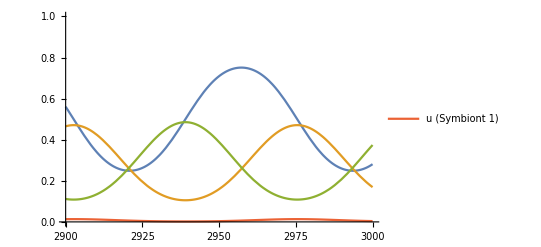

```mathematica
Plot[{uans,vans,pans,mans},{t,2900,3000}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1"}]]
```

Geez doesn’t seem like my mutant (lowest line) is doing too well... How do I pick a threshold after which I say that my mutant has successfully beaten out the resident? Is it just that my mutant is able to grow to a n average frequency higher than 0.01 (the initial frequency)? Or is it that over the course of the simulation the mutant becomes more frequent than the resident?

I spent a fair amount of time thinking about this and did some work on figuring out mutant average frequency. I hit a roadblock when trying to evaluate average specialist 1 frequency, mathematica gets a bit sad when working with interpolating functions

```mathematica
sol=First@NDSolve[num4,{u,v,p,m},{t,0,5000},Method->{"EquationSimplification"->"Residual"}];
funm={m[t]/.sol};
NIntegrate[funm,{t,4600,5000}]/(400);
z[t_?NumericQ]:={v[t]/.sol};
funv = {v[t]/.sol};
funv=DeleteCases[funv,!NumericQ]
NIntegrate[funv,{t,4600,5000}]/(400)
NIntegrate[z[t],{t,4600,5000}]
```

{InterpolatingFunction[…][t]}

NIntegrate::inum: Integrand InterpolatingFunction[{{0.,5000.}},{5,3,1,{13889},{4},0,0,0,0,Automatic,{},{},False},{{0.,«50»}},{{{0.374691},{-0.0154336}},{{0.37469},{-0.0154336}},{{0.374688},{-0.0154337}},«46»,{{0.202082},{-0.0136119}},«13839»},{Automatic}][t] is not numerical at {t} = {4603.18}.

General::stop: Further output of NIntegrate::inum will be suppressed during this calculation.

{1/400 NIntegrate[InterpolatingFunction[{{0., 5000.}}, <>][t],{t,4600,5000}]}

NIntegrate::inum: Integrand z[t] is not numerical at {t} = {4603.18}.

NIntegrate[z[t],{t,4600,5000}]

I spent an inordinate amount of time attempting out how to numerically integrate my specialist host 1 frequency expression, but to little avail.